```mathematica
Clear["Global`*"]
```

## Análise de Fração de Vazio

Inputs: 
- Número de Bolhas
- Raio do Cilindro
- Altura do Cilindro

Outputs:
- Visualização 2D/3D das bolhas no cilindro (o raio das bolhas vai até 0.01r até 0.5r)
- Fração de vazio 
- Área total das bolhas na visualização 2D*

*A área total é uma aproximação da área que seria calculada no experimento, válida para condições experimentais que considerem o caso de um cilindro de raio pequeno.

```mathematica
Cilindro[r_,h_] := ParametricPlot3D[{r Cos[θ],r Sin[θ],z},{θ,0,π},{z,0,h},Mesh->None,PlotStyle->{Opacity[0.8],LightGray}]
```

```mathematica
Cilindro2[r_,h_] := ParametricPlot3D[{r Cos[θ],r Sin[θ],z},{θ,0,2π},{z,0,h},Mesh->None,PlotStyle->{Opacity[0.5],LightGray}]
```

```mathematica
Bolhas[n_, raio_, h_] := 
(bubbles = {{},{}};
For[j=0,j<  n, j++;
rvalue= RandomReal[{0.01raio,0.5raio}];
Rzone= RandomReal[raio-rvalue];
θ = RandomReal[2π];
xvalue = Rzone Cos[θ];
yvalue = Rzone Sin[θ];
zvalue = RandomReal [{rvalue,h-rvalue}];

If[Length[bubbles⟦2⟧]==0, AppendTo[bubbles⟦1⟧,{xvalue,yvalue,zvalue}]; AppendTo[bubbles⟦2⟧,rvalue];j=j+1];

touch={};
For[k=0,k< Length[bubbles⟦1⟧],k++;
pbubble = bubbles⟦1,k⟧;
rbubble = bubbles⟦2,k⟧;
Δx = xvalue - pbubble⟦1⟧;Δy = yvalue - pbubble⟦2⟧;Δz = zvalue - pbubble⟦3⟧;
If[√(Δx^2+Δy^2+Δz^2)> (rvalue + rbubble), AppendTo[touch,0], AppendTo[touch,1]]];

If[FreeQ[touch,1], AppendTo[bubbles⟦1⟧,{xvalue,yvalue,zvalue}]; AppendTo[bubbles⟦2⟧,rvalue],j= j-1]];
AppendTo[bubbles,(Total[Table[4/3 π(bubbles⟦2,i⟧)^3,{i,1,Length[bubbles⟦2⟧]}]])/(π  raio^2  h)];
AppendTo[bubbles,(Total[Table[π(bubbles⟦2,i⟧)^2,{i,1,Length[bubbles⟦2⟧]}]])];
bubbles)
```

```mathematica
VistaBolhas2D[n_,r_,h_]:= (bolhas = Bolhas[n,r,h];
Show[Graphics3D[{Opacity[0.5],Sphere[bolhas⟦1⟧,bolhas⟦2⟧],ViewPoint->{0,- Infinity, 0}}],
Graphics3D[Text[Style[StringForm["Fração de vazio = ``.",bolhas⟦3⟧],15,Plain],{0,0,0.09h}]],Graphics3D[Text[Style[StringForm["Área total = ``.",bolhas⟦4⟧],15,Plain],{0,0,0.04h}]],
Cilindro[r,h]])
```

```mathematica
VistaBolhas3D[n_,r_,h_]:= (bolhas = Bolhas[n,r,h];Show[Graphics3D[{Opacity[0.5],Sphere[bolhas⟦1⟧,bolhas⟦2⟧]}],
Cilindro2[r,h]])
```

```mathematica
Manipulate[f[n,r,h],{f,{VistaBolhas2D}},{n,1,100},{r,1,5},{h,1,10}]
```

```mathematica
VistaBolhas2D[30,1,3]
```

-Graphics3D-

```mathematica
VistaBolhas3D[200,1,3]
```

-Graphics3D-

```mathematica
Bolhas[n_, raio_, h_] := 
(bubbles = {{},{}};
For[j=0,j<  n, j++;
rvalue= RandomReal[{0.01raio,0.5raio}];
Rzone= RandomReal[raio-rvalue];
θ = RandomReal[2π];
xvalue = Rzone Cos[θ];
yvalue = Rzone Sin[θ];
zvalue = RandomReal [{rvalue,h-rvalue}];

If[Length[bubbles⟦2⟧]==0, AppendTo[bubbles⟦1⟧,{xvalue,yvalue,zvalue}]; AppendTo[bubbles⟦2⟧,rvalue];j=j+1];

touch={};
For[k=0,k< Length[bubbles⟦1⟧],k++;
pbubble = bubbles⟦1,k⟧;
rbubble = bubbles⟦2,k⟧;
Δx = xvalue - pbubble⟦1⟧;Δy = yvalue - pbubble⟦2⟧;Δz = zvalue - pbubble⟦3⟧;
If[√(Δx^2+Δy^2+Δz^2)> (rvalue + rbubble), AppendTo[touch,0], AppendTo[touch,1]]];

If[FreeQ[touch,1], AppendTo[bubbles⟦1⟧,{xvalue,yvalue,zvalue}]; AppendTo[bubbles⟦2⟧,rvalue],j= j-1]];
AppendTo[bubbles,(Total[Table[4/3 π(bubbles⟦2,i⟧)^3,{i,1,Length[bubbles⟦2⟧]}]])];
AppendTo[bubbles,(Total[Table[π(bubbles⟦2,i⟧)^2,{i,1,Length[bubbles⟦2⟧]}]])];
bubbles;)
```

```mathematica
Clear[lista]
```

```mathematica
lista = {};
Do[Bolhas[10,1,2];
AppendTo[lista,{bubbles⟦3⟧,bubbles⟦4⟧} ], {i,40}]
```

```mathematica
xy1 = {Total[lista⟦All,1⟧], Total[lista⟦All,2⟧]};
```

```mathematica
lista2 = {};
Do[Bolhas[10,2,4];
AppendTo[lista2,{bubbles⟦3⟧,bubbles⟦4⟧}], {i,40}]
```

```mathematica
xy2 = {Total[lista2⟦All,1⟧], Total[lista2⟦All,2⟧]};
```

```mathematica
lista3 = {};
Do[Bolhas[10,3,6];
AppendTo[lista3,{bubbles⟦3⟧,bubbles⟦4⟧}], {i,40}]
```

```mathematica
xy3 = {Total[lista3⟦All,1⟧], Total[lista3⟦All,2⟧]};
```

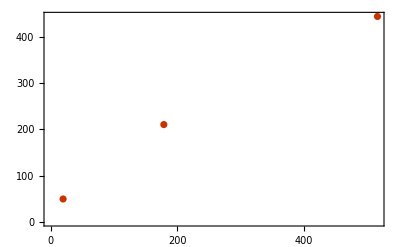

```mathematica
ListPlot[{xy1,xy2,xy3},PlotTheme->"Web"]
```

```mathematica
lista={}
Do[
listalocal = {};
Do[Bolhas[10,i,i];
AppendTo[listalocal,{bubbles⟦3⟧,bubbles⟦4⟧} ], {i,40}];
xy = {Total[listalocal⟦All,1⟧], Total[listalocal⟦All,2⟧]};
AppendTo[lista,xy],
 {i,Range[1,4,0.1]}]
```

{}

```mathematica
lista
```

{{404264.,31738.8},{339396.,28407.6},{394795.,29794.},{287431.,25712.1},{372133.,29519.3},{400863.,30264.3}}

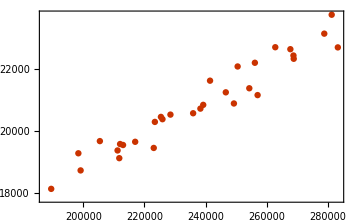

```mathematica
ListPlot[lista,PlotTheme->"Web"]
```

```mathematica
Range[1,2,0.1]
```

{1.,1.1,1.2,1.3,1.4,1.5,1.6,1.7,1.8,1.9,2.}

```mathematica
lista
```

{{254676.,21492.2},{233753.,21186.},{257222.,21234.8},{261889.,21881.},{314991.,23702.2},{240451.,20520.8}}

```mathematica
Grid[%778]
```

254676. | 21492.2
233753. | 21186.
257222. | 21234.8
261889. | 21881.
314991. | 23702.2
240451. | 20520.8

```mathematica
lista={}
Do[
n = 30i;
Bolhas[n,i,i];
listalocal = {};
Do[AppendTo[listalocal,{bubbles⟦3⟧,bubbles⟦4⟧} ], {j,n}];
xy = {Total[listalocal⟦All,1⟧], Total[listalocal⟦All,2⟧]};
AppendTo[lista,xy],
 {i,Range[1,10,0.1]}]
```

{}

$Aborted

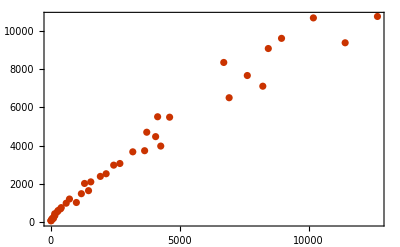

```mathematica
ListPlot[lista,PlotTheme->"Web"]
```

```mathematica
(∑^n)_(i=1) i
```

```mathematica
∑_(i=1)^n i^2
```

1/6 n (1+n) (1+2 n)

```mathematica
Clear[n,i,a]
```

```mathematica
(∑_(i=1)^n i^2)/(∑_(i=1)^n i^3)
```

(2 (1+2 n))/(3 n (1+n))

```mathematica
(∑_(i=1)^n r^2)/(∑_(i=1)^n r^3)
```

1/r

```mathematica
FullSimplify[(a^2+b^2+c^2)/(a^3+b^3+c^3)]
```

(a^2+b^2+c^2)/(a^3+b^3+c^3)

Olha pedro, foi assim que eu pensei que poderia ser a função Do para criar o gráfico para melhorar quanto a questão do dimensionamento. Acho que isso resolve? Até que o gráfico ficou bem bonitinho no final.

```mathematica
lista={}
Do[
listalocal = {};
Do[Bolhas[10,i,i];
AppendTo[listalocal,{bubbles⟦3⟧,bubbles⟦4⟧} ], {i,40}];
xy = {Total[listalocal⟦All,1⟧/(2*i)^3], Total[listalocal⟦All,2⟧]/(2*i)^2};
AppendTo[lista,xy],
 {i,Range[1,4,0.1]}]
```

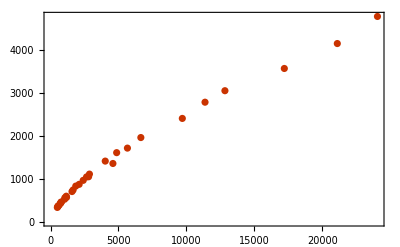

```mathematica
ListPlot[lista,PlotTheme->"Web"]
```

```mathematica
lista={}
Do[
listalocal = {};
Do[Bolhas[40,i,i];
AppendTo[listalocal,{bubbles⟦3⟧,bubbles⟦4⟧} ], {i,40}];
xy = {Total[listalocal⟦All,1⟧/(2*i)^3], Total[listalocal⟦All,2⟧]/(2*i)^2};
AppendTo[lista3,xy],
 {i,Range[1,4,0.1]}]
```

{}

```mathematica
ListPlot[lista,PlotTheme->"Web"]
```

-Graphics-